# Changing Es

```mathematica
Integrate[Cos[ϕ]/(c+G*Cos[ϕ]), ϕ]
```

(ϕ+(2 c ArcTanh[((c-G) Tan[ϕ/2])/(√(-c^2+G^2))])/(√(-c^2+G^2)))/G

# New Initial

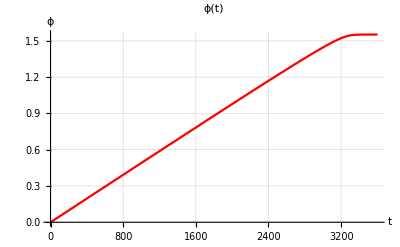

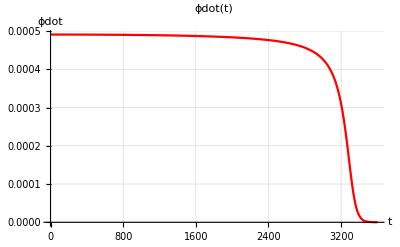

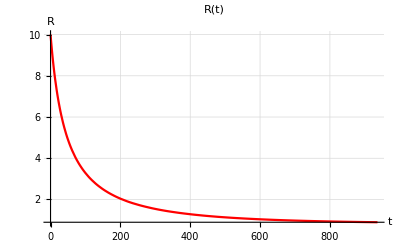

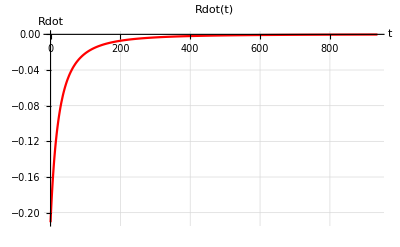

Variable | Value at t = finalTime
RtFinal | 0.896491+0. ⅈ
phiFinal | 0.459012
RtdotFinal | -0.000217907+0. ⅈ
phidotFinal | 0.000489672

```mathematica
ClearAll["Global`*"]

(*Constants*)
r=1;
αt=(1/60)/11250;
αp=(1/(60*64));
P=80*10^3;
Gt=1;
Xt=0.1;
Γt=0;
σt=2000;
Rt0=10;
ph0=0.0;
tmin=0;
tmax=3600;
tminp=0;
finalTime=936;

(*Define phi'*)
phdot[t_]:=(Xt-P αt+Gt Cos[ϕ[t]])/(σt Cos[ϕ[t]]);

(*Solve phi(t)*)
eqns={ϕ'[t]==phdot[t],ϕ[0]==ph0};
sol=NDSolve[eqns,{ϕ},{t,tmin,tmax},Method->{"StiffnessSwitching"},MaxSteps->Infinity];
(*sol=NDSolve[eqns,{ϕ},{t,tmin,tmax},Method->{"StiffnessSwitching"}, MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];*)
phPlot=Plot[Evaluate[ϕ[t]/.sol],{t,tminp,tmax},PlotLabel->"ϕ(t)",AxesLabel->{"t","ϕ"},PlotStyle->Red,PlotRange->All,GridLines->Automatic]
phdotPlot=Plot[Evaluate[phdot[t]/.sol],{t,tminp,tmax},PlotLabel->"ϕdot(t)",AxesLabel->{"t","ϕdot"},PlotStyle->Red,PlotRange->All,GridLines->Automatic]

(*Define phiins[t] from solution*)
phiins[t_]:=Evaluate[ϕ[t]/.sol[[1]]]

(*Define dt[t] placeholder—this is needed!*)
dt[t_]:=Sqrt[1+Rt[t]^2-2*(Cos[phiins[t]]^2-Sin[phiins[t]]*Sqrt[Rt[t]^2-Cos[phiins[t]]^2])];(*Replace this with the actual logic*)(*Define D1,E1,F1 using phiins*)D1[t_]:=Rt[t] (-((4 dt[t])/((-1+dt[t]+Rt[t]) (1+dt[t]+Rt[t])))+(Sqrt[-Cos[phiins[t]]^2+Rt[t]^2]+Sin[phiins[t]])/(Sqrt[-Cos[phiins[t]]^2+Rt[t]^2] Sqrt[Rt[t]^2+(-Cos[2 phiins[t]]+2 Sqrt[-Cos[phiins[t]]^2+Rt[t]^2] Sin[phiins[t]])]))

E1[t_]:=(Cos[phiins[t]] Sqrt[Rt[t]^2+(-Cos[2 phiins[t]]+2 Sqrt[-Cos[phiins[t]]^2+Rt[t]^2] Sin[phiins[t]])])/Sqrt[-Cos[phiins[t]]^2+Rt[t]^2];

F1[t_]:=(4 αp dt[t]^2)/(π 2 (dt[t]^4+(1-Rt[t]^2)^2-2 dt[t]^2 (1+Rt[t]^2)));

(*Evaluate a specific phdot if needed*)
phdotc[t_]:=Evaluate[phdot[t]/.sol[[1]]];

(*Define and solve Rt ODE*)
Rtdot[t_]:=(F1[t]-E1[t] phdotc[t])/D1[t];
eqns1={Rt'[t]==Rtdot[t],Rt[0]==Rt0};

sol1=NDSolve[eqns1,{Rt},{t,tmin,tmax},Method->{"StiffnessSwitching"},MaxSteps->Infinity];
Rtins[t_]:=Evaluate[Rt[t]/.sol1[[1]]]

(*Plot Rt*)
RPlot=Plot[Evaluate[Rt[t]/.sol1],{t,tmin,tmax},PlotLabel->"R(t)",AxesLabel->{"t","R"},PlotStyle->Red,PlotRange->All,GridLines->Automatic]
RtdotPlot=Plot[Evaluate[Rtdot[t]/.sol1],{t,tminp,tmax},PlotLabel->"Rdot(t)",AxesLabel->{"t","Rdot"},PlotStyle->Red,PlotRange->All,GridLines->Automatic]

RtFinal=Rt[finalTime]/.sol1//First//N;
phiFinal=ϕ[finalTime]/.sol//First//N;
RdotFinal=Rtdot[finalTime]/.sol1//First//N;
phdotFinal=phdot[finalTime]/.sol//First//N;


TextGrid[{{"Variable","Value at t = finalTime"},{"RtFinal",RtFinal},{"phiFinal",phiFinal}, {"RtdotFinal",RdotFinal},{"phidotFinal",phdotFinal}},Frame->All,Background->{None,{{LightGray,None}}}]
```

# New Final

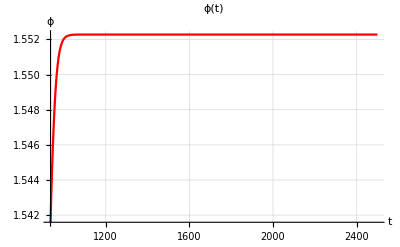

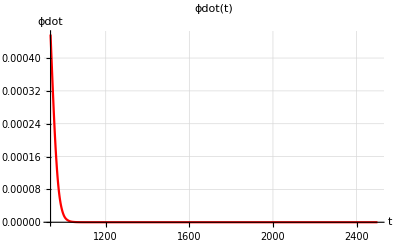

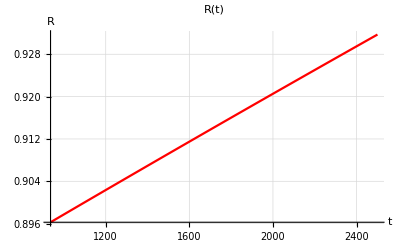

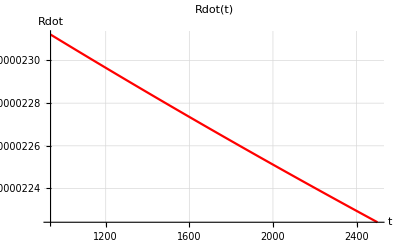

Variable | Value at t = finalTime
RtFinal | 0.896264
phiFinal | 1.54159
RtdotFinal | 0.0000231216
phidotFinal | 0.000457214

```mathematica
ClearAll["Global`*"]

(*Constants*)
r=1;
αt=(1/60)/11250;
αp=(1/(60*64));
P=80*10^3;
Gt=1;
Xt=0.1;
Γt=0;
σt=800;
Rt0=0.896264;
ph0=0.4595;
tmin=936;
tmax=2500;
tminp=936;
finalTime=936;

(*Define phi'*)
phdot[t_]:=(Xt-P αt+Gt Cos[ϕ[t]])/(σt Cos[ϕ[t]]);

(*Solve phi(t)*)
eqns={ϕ'[t]==phdot[t],ϕ[0]==ph0};
sol=NDSolve[eqns,{ϕ},{t,tmin,tmax},Method->{"StiffnessSwitching"},MaxSteps->Infinity];
(*sol=NDSolve[eqns,{ϕ},{t,tmin,tmax},Method->{"StiffnessSwitching"}, MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];*)
phPlot=Plot[Evaluate[ϕ[t]/.sol],{t,tminp,tmax},PlotLabel->"ϕ(t)",AxesLabel->{"t","ϕ"},PlotStyle->Red,PlotRange->All,GridLines->Automatic]
phdotPlot=Plot[Evaluate[phdot[t]/.sol],{t,tminp,tmax},PlotLabel->"ϕdot(t)",AxesLabel->{"t","ϕdot"},PlotStyle->Red,PlotRange->All,GridLines->Automatic]

(*Define phiins[t] from solution*)
phiins[t_]:=Evaluate[ϕ[t]/.sol[[1]]]

(*Define dt[t] placeholder—this is needed!*)
dt[t_]:=Sqrt[1+Rt[t]^2-2*(Cos[phiins[t]]^2+Sin[phiins[t]]*Sqrt[Rt[t]^2-Cos[phiins[t]]^2])];

D1[t_]:=-((4 dt[t] Rt[t])/((-1+dt[t]+Rt[t]) (1+dt[t]+Rt[t])))+(Rt[t] (-Sqrt[-Cos[phiins[t]]^2+Rt[t]^2]+Sin[phiins[t]]))/(Sqrt[Rt[t]^2-r (Cos[2 phiins[t]]+2 Sqrt[-Cos[phiins[t]]^2+Rt[t]^2] Sin[phiins[t]])])

E1[t_]:=( Cos[phiins[t]] Sqrt[Rt[t]^2- ( Cos[2 phiins[t]]+2 Sqrt[- Cos[phiins[t]]^2+Rt[t]^2] Sin[phiins[t]])]);

F1[t_]:=(4 αp dt[t]^2)/(π (dt[t]^4+(1-Rt[t]^2)^2-2 dt[t]^2 (1+Rt[t]^2)))Sqrt[- Cos[phiins[t]]^2+Rt[t]^2];
(*Evaluate a specific phdot if needed*)
phdotc[t_]:=Evaluate[phdot[t]/.sol[[1]]];

(*Define and solve Rt ODE*)
Rtdot[t_]:=(F1[t]-E1[t] phdotc[t])/D1[t];
eqns1={Rt'[t]==Rtdot[t],Rt[tmin]==Rt0};

sol1=NDSolve[eqns1,{Rt},{t,tmin,tmax},Method->{"StiffnessSwitching"},MaxSteps->Infinity];
Rtins[t_]:=Evaluate[Rt[t]/.sol1[[1]]]

(*Plot Rt*)
RPlot=Plot[Evaluate[Rt[t]/.sol1],{t,tmin,tmax},PlotLabel->"R(t)",AxesLabel->{"t","R"},PlotStyle->Red,PlotRange->All,GridLines->Automatic]
RtdotPlot=Plot[Evaluate[Rtdot[t]/.sol1],{t,tminp,tmax},PlotLabel->"Rdot(t)",AxesLabel->{"t","Rdot"},PlotStyle->Red,PlotRange->All,GridLines->Automatic]

RtFinal=Rt[finalTime]/.sol1//First//N;
phiFinal=ϕ[finalTime]/.sol//First//N;
RdotFinal=Rtdot[finalTime]/.sol1//First//N;
phdotFinal=phdot[finalTime]/.sol//First//N;


TextGrid[{{"Variable","Value at t = finalTime"},{"RtFinal",RtFinal},{"phiFinal",phiFinal}, {"RtdotFinal",RdotFinal},{"phidotFinal",phdotFinal}},Frame->All,Background->{None,{{LightGray,None}}}]
```